# 8. QRDecomposition

## Math Libraries

Math libraries (BLAS, MKL, ...) are portable, fast, and an all round good idea!

We are about to see that subtle algorithmic differences can significantly impact stability and performance!

Real QR codes would never do GS (7.1) when MGS (8.1) is better and almost the same amount of work. Both treat R as the main product and Q as a byproduct.

Most of the time Q is the thing folks want and R is just thrown away. In this case the Householder algorithm we are going to talk about next which has Q as the main target gives more nearly perfectly orthogonal matrices.

## Modified Gram-Schmidt

Here is our implementation of GS 7.1

```mathematica
MyGramSchmidt[A_]:= Module[{m,n,Q,R,v},
{m,n}=Dimensions[A];
(* Set up Storage *)
Q=0*A; R=ConstantArray[0,{n,n}];
(* Loop through columns *)
Do[
(* Grab next column *)
v=A⟦All,j⟧;
(* project out previous columns *)
Do[
R⟦i,j⟧=v.Q⟦All,i⟧;
v=v-R⟦i,j⟧ Q⟦All,i⟧,
{i,1,j-1}];
(* Scale and save orthogonalized columns *)
R⟦j,j⟧=Norm[v];
Q⟦All,j⟧=v/R⟦j,j⟧;,
{j,1,n}];
{Q,R}]
```

Here is an implementation of Modified GS 8.1

```mathematica
MyModifiedGramSchmidt[A_]:= Module[{m,n,Q,R,V},
{m,n}=Dimensions[A];
V=A;Q=0*A; R=ConstantArray[0,{n,n}];
Do[
R⟦i,i⟧=Norm[V⟦All,i⟧];
Q⟦All,i⟧=V⟦All,i⟧/R⟦i,i⟧;
Do[
R⟦i,j⟧=Q⟦All,i⟧.V⟦All,j⟧;
V⟦All,j⟧=V⟦All,j⟧-R⟦i,j⟧ Q⟦All,i⟧,
{j,i+1,n}],
{i,1,n}];
{Q,R}]
```

Testing and comparing the two versions! Both work.

```mathematica
427/4.
```

106.75

```mathematica
{m,n}={744,107};
A=RandomReal[{-1,1},{m,n}];
TableForm[
Table[
time=AbsoluteTiming[{Q,R}=qr[A];]⟦1⟧;{qr,time,Norm[Qᵀ.Q-IdentityMatrix[n]],Norm[A-Q.R]},
{ qr,{MyGramSchmidt,MyModifiedGramSchmidt}}],
TableHeadings->{None,{"Algorithm","Sec","Orth Res","Residual"}}
]
```

Algorithm | Sec | Orth Res | Residual
MyGramSchmidt | 0.163696 | 8.85581×10^-16 | 8.62505×10^-15
MyModifiedGramSchmidt | 0.2797 | 8.85581×10^-16 | 8.62505×10^-15

```mathematica
4.06/0.2797
```

14.5156

Algorithm | Sec | Orth Res | Residual
MyGramSchmidt | 1.79292 | 1.72002×10^-15 | 2.03523×10^-14
MyModifiedGramSchmidt | 4.06135 | 1.72002×10^-15 | 2.03523×10^-14

Just for comparison!

```mathematica
time=AbsoluteTiming[{Q,R}=QRDecomposition[A];]⟦1⟧;
Q=Qᵀ; 
{time,Norm[Qᵀ.Q-IdentityMatrix[n]],Norm[A-Q.R]}
```

{0.0083984,9.947×10^-16,1.18648×10^-14}

## Modified vs Classical Gram-Schmidt

One of them is better! It is subtle but it is real!  There are two main problems: small entries in R can be computed inaccurately and the Q could lose orthogonality due to only 16 digits of computer arithmetic!  MKS is better at resolving R accurately (we will pay more attention to this later) but both struggle to generate fully accurate orthogonal matrices  when the going gets tough

Random matrices are unlikely to highlight these problems.  We need to make tricksy matrices.

#### Nearly Parallel Columns

Both of our Gram-Schmidt algorithms struggle with nearly parallel columns.   The important thing is that better algorithms are used in built-in QR calls.

```mathematica
m=16;
ϵ =0.000001;
{u,v}= RandomReal[{-1,1},{2,m}];
A=KroneckerProduct[u,v]+ϵ RandomReal[{-1,1},{m,m}];
MatrixPlot[A];
{Timing[{Qgs,Rgs}=MyGramSchmidt[A];],
Timing[{Qmgs,Rmgs}=MyModifiedGramSchmidt[A];],
Timing[{Q,R}=QRDecomposition[A];Q=Qᵀ;]}
Map[{Norm[#⟦1⟧.#⟦1⟧ᵀ-IdentityMatrix[m]],Norm[A-#⟦1⟧.#⟦2⟧]}&,
{{Q,R},{Qgs,Rgs},{Qmgs,Rmgs}}]
```

{{0.,Null},{0.,Null},{0.,Null}}

{{9.72068×10^-16,1.75882×10^-15},{1.68773×10^-9,3.32855×10^-16},{1.68773×10^-9,3.32855×10^-16}}

This better algorithm designs and accumulates a sequence of orthogonal matrices Q_1,Q_2,… at each stage!  The simplest version of this is a “Householder” reflector.

## Householder Reflections

We have already seen that H=I-2P is a symmetric orthogonal matrix if P is an orthogonal projection.   Since it is straight-forward lets do it again.  Assume P=Pᵀ and P.P=P then
	Hᵀ.H=(I-2P)ᵀ.(I-2P)=(I-2P).(I-2P)=I-2P-2P+4P.P=I-4P+4p=I.
A Householder reflection chooses the first projection P_1 so that H_1=I-2 P_1satisfies H_1.a_1=±||a_1||e_1. You then repeat  the process (with some bookkeeping) until you run out of columns!

Given a we need to choose P to make 
	(I-2 P).a=±||a||e_1
or equivalently
	-2 P.a=-a±||a||e_1
or equivalently
	2 P.a=a∓||a||e_1
If v is a unit vector the projection P=I-v⊗v has m-1 Degrees Of Freedom (DOF). It is possible to choose v to do what we want!  We want v to satisfy
	2 (I-v⊗v).a=a∓||a||e_1
or equivalently
	2 a-2v (v.a)=a∓||a||e_1
or equivalently
	-2v (v.a)=-a∓||a||e_1 ⟹ v(v.a)=(1/2)(a±||a||e_1)
In words, v is a unit vector parallel to a±||a||e_1.

It is easy to check that this works.

```mathematica
m=12;
a=RandomReal[{-1,1},m];
v=a; 
v⟦1⟧=v⟦1⟧+Norm[a];
v=v/Norm[v];
P=IdentityMatrix[m]-KroneckerProduct[v,v];
H=IdentityMatrix[m]- 2 P;
Norm[H.Hᵀ -IdentityMatrix[m]]
Chop[H.a]
```

4.82346×10^-16

{2.3199,0,0,0,0,0,0,0,0,0,0,0}

## Plotting Complex Stuff!

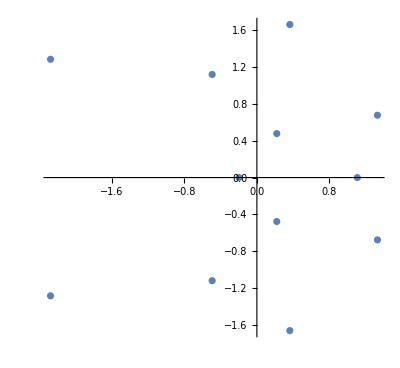

```mathematica
m=12;
A=RandomReal[{-1,1},{m,m}];
ListPlot[ ReIm[Eigenvalues[A]],
AspectRatio->Automatic]
```